## LIBR

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## APPLICATIONS

## tmp-movie_protocol_IN-DEV

```mathematica
(*
Table[gLine[{k,If[k<=10,k,11-Mod[k,10]]},Color->Cyan,Thickness->0.0025],{k,2,19}]//toGL//gr
 f[x_,y_]:=Table[gLine[{x,y},pGon[128][[k]],Color->Gray,Thickness->0.0025],{k,1,128}]//toGL//gr
f[-0.5,-0.5]
gAnimation=ConstantArray[0,101]
Table[{k,k},{k,-0.5,0.5,0.01}]//Length
For[k=1,k<=101,k++,gAnimation[[k]]=f[-0.51+ k/100,-0.51+ k/100]]
Export["movie.avi",gAnimation]
*)
```

## DEV

## Three Reflections Theorem

### Introduction

-Graphics-

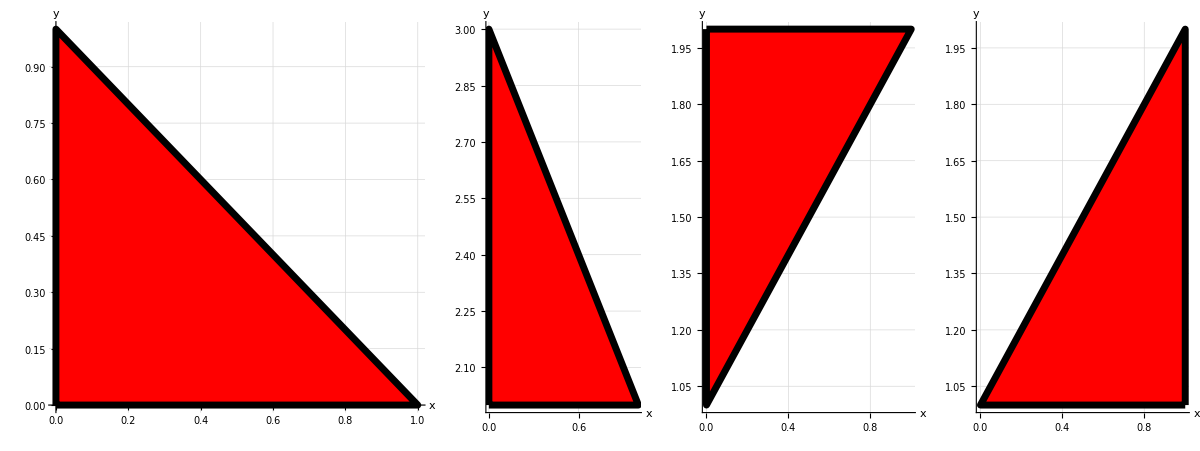

```mathematica
GraphicsRow[
{
gPolygon[{{0,0},{1,0},{0,1}}]//toGL//gr1,
tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}]//toGL//gr1,
rot3[tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}],{3/2Pi/1,{0,2}}]//toGL//gr1,
ref3[rot3[tra3[gPolygon[{{0,0},{1,0},{0,1}}],{0,2}],{3/2Pi/1,{0,2}}],{{-1,1},{0,1}}]//toGL//gr1
}
]
```

### Translation :> Reflections

```mathematica
traM:={{1,0,0},{0,1,2},{0,0,1}}
ptsM:={{0,1,0},{0 ,0,1},{1,1,1}}

traM//mf
ptsM//mf
```

(1 | 0 | 0
0 | 1 | 2
0 | 0 | 1)

(0 | 1 | 0
0 | 0 | 1
1 | 1 | 1)

```mathematica
traM.ptsM//mf
```

(0 | 1 | 0
2 | 2 | 3
1 | 1 | 1)

### tmp

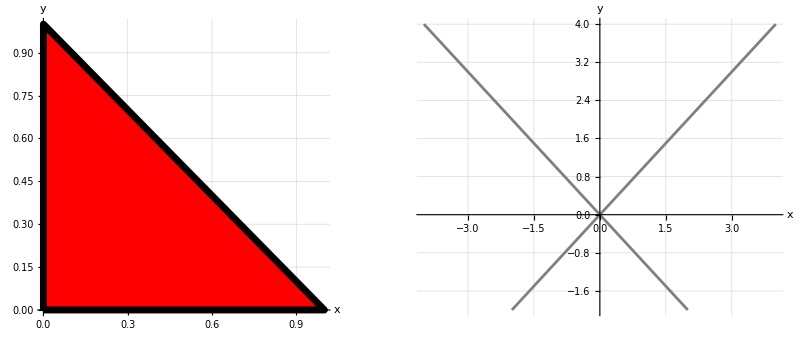

{1,1}

{-1,1}

```mathematica
figdemo:=gPolygon[{{0,0},{1,0},{0,1}}];
GraphicsRow[
{
figdemo//toGL//gr1,
{
gLine[{-2,-2},{4,4},Color->Gray, Thickness->0.005]//toGL,
gLine[{2,-2},{-4,4},Color->Gray, Thickness->0.005]//toGL}//gr1
}
]
({4,4}-{-2,-2})/6
({-4,4}-{2,-2})/6
```

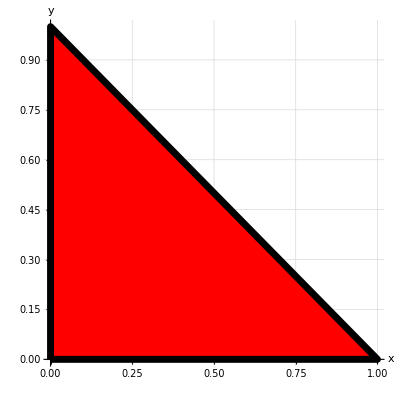

```mathematica
figdemo//toGL//gr1
```

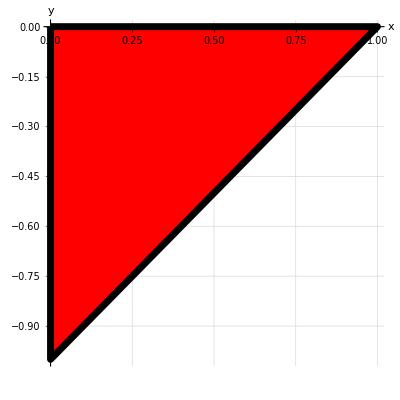

```mathematica
ref3[figdemo,{{0,1},{0,0}}]//toGL//gr1
```

```mathematica
mat1:={{0,-3},{3,0}}
mat2:={{0,-3,-3},{3,0,3},{3,-3,0}}
```

```mathematica
mat2//mf
-Transpose[mat2]//mf
```

(0 | -3 | -3
3 | 0 | 3
3 | -3 | 0)

(0 | -3 | -3
3 | 0 | 3
3 | -3 | 0)

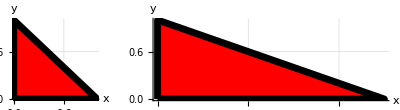

```mathematica
GraphicsRow[
{
gPolygon[{{0,0},{1,0},{0,1}}]//toGL//gr1,
tra3[gPolygon[{{0,0},{1,0},{0,1}}],{2,0}]//toGL//gr1
}
]
```

```mathematica
Options[gPoint]
```

{Color→RGBColor[1, 0, 0],Opacity→1,PointSize→0.0125}

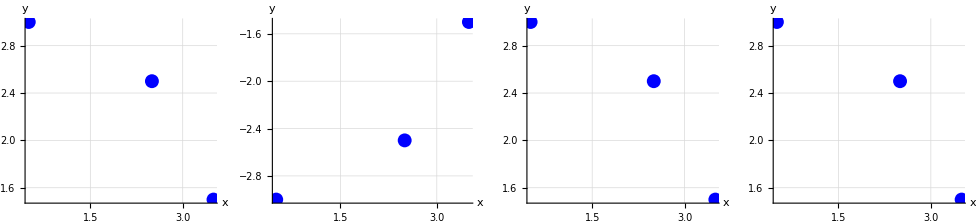

```mathematica
GraphicsRow[
{
tra3[gPoint[{{0.5,3.0},{2.5,2.5},{3.5,1.5}},Color->Blue,PointSize->0.025],{0,0}]//toGL//gr1,
ref3[tra3[gPoint[{{0.5,3.0},{2.5,2.5},{3.5,1.5}},Color->Blue,PointSize->0.025],{0,0}],{{0,1},{0,0}}]//toGL//gr1,
ref3[ref3[tra3[gPoint[{{0.5,3.0},{2.5,2.5},{3.5,1.5}},Color->Blue,PointSize->0.025],{0,0}],{{0,1},{0,0}}],{{0,1},{0,0}}]//toGL//gr1,

ref3[ref3[tra3[gPoint[{{0.5,3.0},{2.5,2.5},{3.5,1.5}},Color->Blue,PointSize->0.025],{0,0}],{{0,1},{0,0}}],{{0,1},{0,0}}]//toGL//gr1

}
]

ref3[tra3[gPoint[{{0.5,3.0},{2.5,2.5},{3.8,3.8}},Color->Cyan,PointSize->0.05],{0,0}],{{-1,1},{0,0}}]//toGL//gr1;
tra3[gPoint[{{1.0,1.0},{2.5,2.5},{3.5,3.5}},Color->Cyan,PointSize->0.05],{1,1}]//toGL//gr1;
```

```mathematica
ftest[x_,y_]:=2x+y^2
ftest[2,2]
fResult
```

8

```mathematica
1+24/60+51/60^2+10/60^3//N
```

1.41421

```mathematica
√2//N
```

1.41421

```mathematica
(6+42/6)/2//N
```

6.5

```mathematica
(6.5+42/6.5)/2//N
```

6.48077

```mathematica
√42//N
```

6.48074

```mathematica
((6.5+42/6.5)/2+42/((6.5+42/6.5)/2))/2//N
```

6.48074

```mathematica
√((.5)^2+(.5)^2)
```

0.707107

## tmp

## Cubic

```mathematica
x^3+a x^2+b x+c

Collect[x^3+a x^2+b x+c/.{x:>y-a/3}//Simplify,y]
Collect[Collect[x^3+a x^2+b x+c/.{x:>y-a/3}//Simplify,y]/.{y:>z- (-a^2/3+b)/(3z)}//Simplify ,z]
Collect[Collect[Collect[x^3+a x^2+b x+c/.{x:>y-a/3}//Simplify,y]/.{y:>z- (-a^2/3+b)/(3z)}//Simplify ,z] z^3,z]
Collect[Collect[Collect[x^3+a x^2+b x+c/.{x:>y-a/3}//Simplify,y]/.{y:>z- (-a^2/3+b)/(3z)}//Simplify ,z] z^3,z]/.{z:>w^(1/3)}
```

c+b x+a x^2+x^3

(2 a^3)/27-(a b)/3+c+(-a^2/3+b) y+y^3

1/729 (54 a^3-243 a b+729 c)+(a^6-9 a^4 b+27 a^2 b^2-27 b^3)/(729 z^3)+z^3

1/729 (a^6-9 a^4 b+27 a^2 b^2-27 b^3)+1/729 (54 a^3-243 a b+729 c) z^3+z^6

1/729 (a^6-9 a^4 b+27 a^2 b^2-27 b^3)+1/729 (54 a^3-243 a b+729 c) w+w^2

```mathematica
Solve[1/729 (a^6-9 a^4 b+27 a^2 b^2-27 b^3)+1/729 (54 a^3-243 a b+729 c) w+w^2==0,w]
```

{{w→1/54 (-2 a^3+9 a b-27 c-3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))},{w→1/54 (-2 a^3+9 a b-27 c+3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))}}

```mathematica
(1/729 (a^6-9 a^4 b+27 a^2 b^2-27 b^3)+1/729 (54 a^3-243 a b+729 c) w+w^2)/.w:>1/54 (-2 a^3+9 a b-27 c-3 √3 √(-a^2 b^2+4 b^3+4 a^3 c-18 a b c+27 c^2))//Simplify
```

0